```mathematica
a=Import["~/fw-517-2025-02-28/ACS_LOG_2025-02-26_H12_M22_S01.csv","CSV"];
```

```mathematica
a[[Length[a]]]
```

{2025 Feb 28 17:03:33.985,189693.,200399.,23.9375,0.,0.,22.125,21.875,-15.1875,-1.875,22.125,-4.4375,-2.125,0}

```mathematica
a[[1]]
```

{2025 Feb 26 12:22:01.489,0.01,200437.,22.6875,0.,0.,21.125,20.875,-15.,20.9375,20.875,15.8125,19.0625,0}

```mathematica
Length[a[[1]]]
```

14

```mathematica
a[[Length[a]]]
```

{2025 Feb 28 17:03:33.985,189693.,200399.,23.9375,0.,0.,22.125,21.875,-15.1875,-1.875,22.125,-4.4375,-2.125,0}

```mathematica
a[[1,2]]
```

0.01

```mathematica
a[[1,9]]
```

-15.

```mathematica
a[[Length[a],9]]
```

-15.1875

```mathematica
redline={{a[[1,2]],0},{a[[Length[a],2]],0}}
```

{{0.01,0},{189693.,0}}

```mathematica
greenline={{a[[1,2]],-15},{a[[Length[a],2]],-15}}
```

{{0.01,-15},{189693.,-15}}

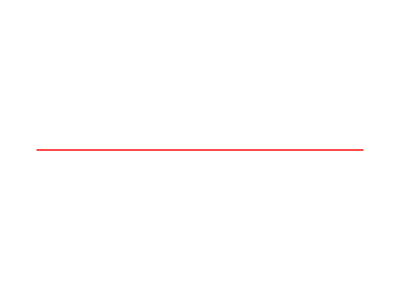

```mathematica
RedLine=Show[Graphics[{Hue[1],Line[redline]}]]
```

```mathematica
?LineWidth
```

Missing[UnknownSymbol,LineWidth]

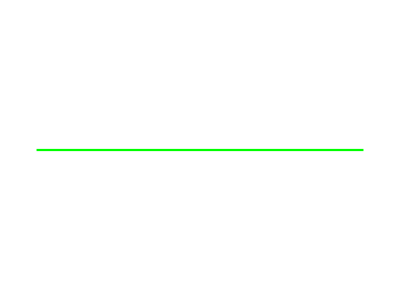

```mathematica
GreenLine=Show[Graphics[{Thickness[0.004],Green,Line[blueline]}]]
```

```mathematica
?Color
```

Missing[UnknownSymbol,Color]

```mathematica
Graphics[{}]
```

```mathematica
b=Transpose[a];
```

```mathematica
c1=Table[{b[[2,i]],b[[9,i]]},{i,Length[b[[2]]]}];
```

```mathematica
g1=ListPlot[c1,ImageSize->1000,PlotRange->{-20,0},Axes->False,Frame->True]
```

-Graphics-

```mathematica
Show[g1,RedLine,GreenLine]
```

-Graphics-

```mathematica
c2=Table[{b[[2,i]],b[[10,i]]},{i,Length[b[[2]]]}];
```

```mathematica
g2=ListPlot[c2,ImageSize->1000,PlotRange->All,Axes->False,Frame->True]
```

-Graphics-

```mathematica
Show[g2,RedLine]
```

-Graphics-

```mathematica
c4=Table[{b[[2,i]],b[[12,i]]},{i,Length[b[[2]]]}];
```

```mathematica
g4=ListPlot[c4,ImageSize->1000,PlotRange->All,Axes->False,Frame->True]
```

-Graphics-

```mathematica
Show[g4,RedLine]
```

-Graphics-

```mathematica
c5=Table[{b[[2,i]],b[[13,i]]},{i,Length[b[[2]]]}];
```

```mathematica
g5=ListPlot[c5,ImageSize->1000,PlotRange->All,Axes->False,Frame->True]
```

-Graphics-

```mathematica
Show[g5,RedLine]
```

-Graphics-